#### X^1 Σ_g^+ Potential

(in cm^-1 and Å)

```mathematica
Ns = 4.53389;
u1 = -0.638904880*10^4;
u2 = 0.112005361*10^7;
rsr = 3.126;
rlr = 11.000;
b =-0.13;
rm = 4.209912706;
acf = {-3993.592873, 0, 0.282069372972346137*10^5,0.560425000209256905*10^4, -0.423962138510562945*10^5,-0.598558066508841584*10^5,-0.162613532034769596*10^5,
-0.405142102246254944*10^5, 0.195237415352729586*10^6,0.413823663033582852*10^6,−0.425543284828921501*10^7,0.546674790157210198*10^6,0.663194778861331940*10^8,−0.558341849704095051*10^8,-0.573987344918535471*10^9,0.102010964189156187*10^10,0.300040150506311035*10^10,-0.893187252759830856*10^10,-0.736002541483347511*10^10, 0.423130460980355225*10^11,-0.786351477693491840*10^10,-0.102470557344862152*10^12,0.895155811349267578*10^11, 0.830355322355692902*10^11,-0.150102297761234375*10^12, 0.586778574293387070*10^11 };
C6 = 0.2270032*10^8;
C8 = 0.7782886 *10^9;
C10 = 0.2868869*10^11;
C26 = 0.2819810*10^26;
Aex = 0.1317786*10^5;
gamma = 5.317689;
beta = 2.093816;
```

Intermediate Potential

```mathematica
ξ[r_]:= (r-rm)/(r+b rm);
uIR[r_]:= Sum[acf[[i+1]]*(ξ[r])^i,{i,0,Length[acf]-1}];
```

Short-Range Potential

```mathematica
uSR[r_]:= u1 +u2/r^Ns;
```

Long-Range Potential

```mathematica
uLR[r_]:= -C6/r^6-C8/r^8-C10/r^10-C26/r^26-Aex r^gamma Exp[-beta r];
```

Full Potential

```mathematica
Singlet[r_]:=Piecewise[{{uSR[r],0<r≤rsr},{uIR[r],rsr<r<rlr},{uLR[r],rlr≤ r}}];
```

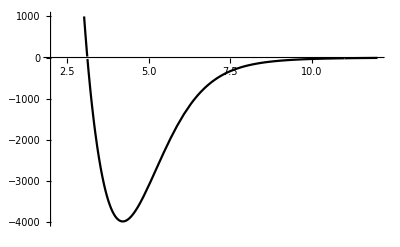

```mathematica
Plot[Singlet[r],{r,2,12},PlotRange->{-4005,1000}]
```

#### a^3 Σ_u^+ Potential

```mathematica
Ns3 = 4.5338950;
u13=-0.619088543*10^3;
u23 = 0.956231677*10^6;
r3sr = 5.07;
b3 =-0.33;
rm3 = 6.0933451;
a3cf = {−241.503352,−0.672503402304666542,0.195494577140503543*10^4,−0.141544168453406223*10^4,−0.221166468149940465*10^4,0.165443726445793004*10^4,−0.596412188910614259*10^4,
0.654481694231538040*10^4,0.261413416681972012*10^5,−0.349701859112702878*10^5,−0.328185277155018630*10^5, 0.790208849885562522*10^5,−0.398783520249289213*10^5};
```

```mathematica
ξ3[r_]:= (r-rm3)/(r+b3 rm3);
uIR3[r_]:= Sum[a3cf[[i+1]]*(ξ3[r])^i,{i,0,Length[a3cf]-1}];
uSR3[r_]:= u13 +u23/r^Ns3;
uLR3[r_]:= -C6/r^6-C8/r^8-C10/r^10-C26/r^26+Aex r^gamma Exp[-beta r];
```

```mathematica
gamma
```

5.31769

```mathematica
Aex
```

13177.9

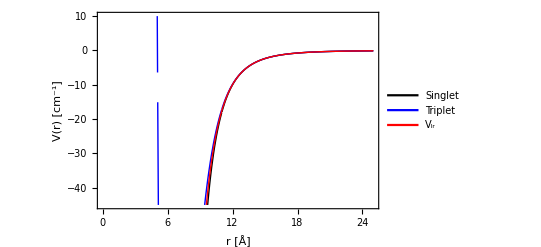

```mathematica
Triplet[r_]:=Piecewise[{{uSR3[r],0<r≤r3sr},{uIR3[r],r3sr≤ r≤ rlr},{uLR3[r],rlr≤ r}}];
Plot[{Legended[Singlet[r],"Singlet"],Legended[Triplet[r],"Triplet"],Legended[-C6/r^6-C8/r^8-C10/r^10,"V_lr"]},{r,0,25},PlotRange->{-45,10},PlotTheme->None,PlotStyle->{Black,Blue,Red,Green},Frame->True,FrameLabel->{"r [Å]","V(r) [cm^-1]"}]
```

#### Convert to Atomic Units

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
```

```mathematica
Rmax=700;
Rmin=0.005;
NR =10000;
dR=(Rmax-Rmin)/NR;
RGrid =Table[Rmin+dR i,{i,1,NR}];
```

```mathematica
SingletRbAU[r_]:=Singlet[r/AngstrominBohr]*invcminHartree
TripletRbAU[r_]:=Triplet[r/AngstrominBohr]*invcminHartree
```

```mathematica
SingletNewdat = Table[{RGrid[[i]]*AngstrominBohr,Singlet[RGrid[[i]]]*invcminHartree},{i,1,NR}];
TripletNewdat = Table[{RGrid[[i]]*AngstrominBohr,Triplet[RGrid[[i]]]*invcminHartree},{i,1,NR}];
```

```mathematica
SingletNew = Interpolation[SingletNewdat];
TripletNew=Interpolation[TripletNewdat];
```

```mathematica
(*Plot[{SingletNew[r],TripletNew[r],(-C6*AngstrominBohr^6*invcminHartree)/r^6-(C8*AngstrominBohr^8*invcminHartree)/r^8-(C10*AngstrominBohr^10*invcminHartree)/r^10},{r,3,20},PlotRange->{-0.040,0.040},PlotTheme->None,PlotStyle->{Black,Black,Red,Green},Frame->True,FrameLabel->{"r [bohr]","V(r) [Hartree]"},GridLines->Automatic,LabelStyle->Medium]*)
```

```mathematica
(*sgdat =Import["/Users/niravmehta/Documents/GitHub/LiScattering/fort.10"];
tpdat =Import["/Users/niravmehta/Documents/GitHub/LiScattering/fort.30"];*)
```

```mathematica
(*sgfun = Interpolation[sgdat];*)
```

Interpolation::inauto: The function value at each grid point must be specified. It cannot be omitted or given as "Automatic".

```mathematica
(*tpfun=Interpolation[tpdat];*)
```

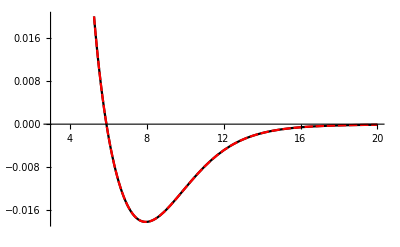

```mathematica
(*Plot[{SingletNew[r],sgfun[r]},{r,3,20},PlotStyle->{Black,Red}]*)
```

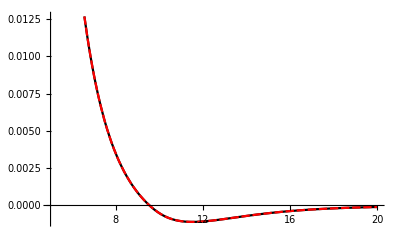

```mathematica
(*Plot[{TripletNew[r],tpfun[r]},{r,5,20},PlotStyle->{Black,Red}]*)
```

```mathematica
amu = 1822.88848621171;
massRb87 = 86.909180527*amu;
massRb85 =84.911789738*amu;
```

```mathematica
μRb87 = massRb87/2;
μRb85 = massRb85/2;
```

```mathematica
amu=(1.6605390666 10^-27)/(9.109383701528 10^-31)
```

```mathematica
1822.88848621171
```

```mathematica
(5.48579909065 10^-4)^-1
```

```mathematica
1822.8884862086923
```

```mathematica
CalcCotanDelta[Εtest_,rmax_,rmin_,μ_,U_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2,u},
r1=0.95 rmax;
r2=0.99rmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[r]+U[r] u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-6},u,{r,rmin,rmax},AccuracyGoal->20];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]
```

```mathematica
CalcERE[rmax_,rmin_,ΕMin_,ΕMax_,μ_,U_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcCotanDelta[Εtest,rmax,rmin,μ,U]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
CalcERE[3400,3,1nkinHartree,2 nkinHartree,μRb87,SingletRbAU]
```

{90.1616,177.716,{{5.01704×10^-10,-0.0110911},{5.51875×10^-10,-0.0110911},{6.02045×10^-10,-0.0110911},{6.52216×10^-10,-0.0110911},{7.02386×10^-10,-0.0110911},{7.52557×10^-10,-0.0110911},{8.02727×10^-10,-0.0110911},{8.52898×10^-10,-0.0110911},{9.03068×10^-10,-0.0110911},{9.53239×10^-10,-0.0110911},{1.00341×10^-9,-0.0110911}}}

```mathematica
CalcERE[3400,3,1nkinHartree,2 nkinHartree,μRb87,TripletRbAU]
```

{98.8669,137.136,{{5.01704×10^-10,-0.0101146},{5.51875×10^-10,-0.0101146},{6.02045×10^-10,-0.0101146},{6.52216×10^-10,-0.0101146},{7.02386×10^-10,-0.0101146},{7.52557×10^-10,-0.0101146},{8.02727×10^-10,-0.0101145},{8.52898×10^-10,-0.0101145},{9.03068×10^-10,-0.0101145},{9.53239×10^-10,-0.0101145},{1.00341×10^-9,-0.0101145}}}

#### Hyperfine and Zeeman Structure of ^87 Rb and ^85 Rb

Hyperfine constant (MHz/h), electronic gyromagnetic ratio, nuclear gyromagnetic ratio, electronic spin, nuclear spin

```mathematica
Rb87AMHz = 3417.3413064215;
Rb85AMHz = 1011.9108132;
Rb87gi = -0.000995141410;
Rb85gi = -0.00029364006;
Rb87gs = 2.002319313470;
Rb85gs = Rb87gs;
Rb87s = 1/2;
Rb85s = Rb87s;
Rb87i = 3/2;
Rb85i = 5/2;
```

Hyperfine bases for rubidium isotopes

```mathematica
Rb87HFbasis = Flatten[Table[Table[{f, mf},{mf,-f,f}],{f,1,2}],1]
```

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
Rb85HFbasis=Flatten[Table[Table[{f, mf},{mf,-f,f}],{f,2,3}],1]
```

{{2,-2},{2,-1},{2,0},{2,1},{2,2},{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3}}

Nuclear and Bohr Magnetons (MHz/G)

```mathematica
μb = (9.27*10^-24)/(6.626*10^-34)*10^-10
(*μn = (5.0507837461*10^-27)/(6.626*10^-34)*10^-10*)
```

1.39903

Converting to Atomic Units

```mathematica
Rb87ATHz = Rb87AMHz*10^-6;
Rb85ATHz = Rb85AMHz*10^-6;
Rb87Ainvcm = (Rb87ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Rb85Ainvcm = (Rb85ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Rb87AH = Rb87Ainvcm*invcminHartree;
Rb85AH = Rb85Ainvcm*invcminHartree;
μbTHz = μb *10^-6;
μnTHz = μn*10^-6;
μbinvcm = (μbTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μninvcm = (μnTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μbH=μbinvcm*invcminHartree;
μnH=μninvcm*invcminHartree;
```

```mathematica
Hhf[A_,i_,s_,f_,ℏ_]:= A/2 ℏ^2(f(f+1)-s(s+1)-i(i+1));
```

```mathematica
Hz[fp_,mp_,f_,m_,gi_,gs_,s_,i_,B_]:= gs μbH B √((2 fp +1)(2f +1)) Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μbH B √((2 fp +1)(2f +1)) Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

Rubidium-87

```mathematica
HhfRb87Table=Table[Hhf[Rb87AH,Rb87i,Rb87s,Rb87HFbasis[[j,1]],1]KroneckerDelta[j,jp],{j,1,8},{jp,1,8}];
```

```mathematica
HzRb87Table[B_]:= Table[Hz[Rb87HFbasis[[jp,1]],Rb87HFbasis[[jp,2]],Rb87HFbasis[[j,1]],Rb87HFbasis[[j,2]],Rb87gi,Rb87gs,Rb87s,Rb87i,B],{j,1,8},{jp,1,8}];
```

```mathematica
HRb87[B_]:= HzRb87Table[B] + HhfRb87Table;
```

```mathematica
Rb87AtomEigenSystem[B_]:=Sort[Transpose[Eigensystem[HRb87[B]]]]
Rb87AtomEth[B_]:=Table[Rb87AtomEigenSystem[B][[i]][[1]],{i,1,8}]
Rb87EigenSystem[B_]:=Sort[Eigenvalues[HRb87[B]]];
```

```mathematica
(*Plot[{Rb87EigenSystem[B][[1]],Rb87EigenSystem[B][[2]],Rb87EigenSystem[B][[3]],Rb87EigenSystem[B][[4]],Rb87EigenSystem[B][[5]],Rb87EigenSystem[B][[6]],Rb87EigenSystem[B][[7]],Rb87EigenSystem[B][[8]]},{B,1,2000}, Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},ImageSize->Large,LabelStyle->Large ]*)
```

```mathematica
hartreetoK = 3.1577502480407*10^5;
```

```mathematica
(*Plot[{Rb87EigenSystem[B][[1]]*hartreetoK,Rb87EigenSystem[B][[2]]*hartreetoK,Rb87EigenSystem[B][[3]]*hartreetoK,Rb87EigenSystem[B][[4]]*hartreetoK,Rb87EigenSystem[B][[5]]*hartreetoK,Rb87EigenSystem[B][[6]]*hartreetoK,Rb87EigenSystem[B][[7]]*hartreetoK,Rb87EigenSystem[B][[8]]*hartreetoK},{B,1,2000}, Frame->True,FrameLabel->{"B [G]","Energy [K]"},ImageSize->Large,LabelStyle->Large ]*)
```

Rubidium-85

```mathematica
HhfRb85Table=Table[Hhf[Rb85AH,Rb85i,Rb85s,Rb85HFbasis[[j,1]],1]KroneckerDelta[j,jp],{j,1,Length[Rb85HFbasis]},{jp,1,Length[Rb85HFbasis]}];
HzRb85Table[B_]:= Table[Hz[Rb85HFbasis[[jp,1]],Rb85HFbasis[[jp,2]],Rb85HFbasis[[j,1]],Rb85HFbasis[[j,2]],Rb85gi,Rb85gs,Rb85s,Rb85i,B],{j,1,Length[Rb85HFbasis]},{jp,1,Length[Rb85HFbasis]}];
HRb85[B_]:= HzRb85Table[B] + HhfRb85Table;
Rb85AtomEigenSystem[B_]:=Sort[Transpose[Eigensystem[HRb85[B]]]]
Rb85AtomEth[B_]:=Table[Rb85AtomEigenSystem[B][[i]][[1]],{i,1,Length[Rb85HFbasis]}]
Rb85EigenSystem[B_]:=Sort[Eigenvalues[HRb85[B]]];
```

```mathematica
(*Plot[{Rb85EigenSystem[B][[1]]*hartreetoK,Rb85EigenSystem[B][[2]]*hartreetoK,Rb85EigenSystem[B][[3]]*hartreetoK,Rb85EigenSystem[B][[4]]*hartreetoK,Rb85EigenSystem[B][[5]]*hartreetoK,Rb85EigenSystem[B][[6]]*hartreetoK,Rb85EigenSystem[B][[7]]*hartreetoK,Rb85EigenSystem[B][[8]]*hartreetoK,Rb85EigenSystem[B][[9]]*hartreetoK,Rb85EigenSystem[B][[10]]*hartreetoK,Rb85EigenSystem[B][[11]]*hartreetoK,Rb85EigenSystem[B][[12]]*hartreetoK},{B,1,1000}, Frame->True,FrameLabel->{"B [G]","Energy [K]"},ImageSize->Large,LabelStyle->Large ]*)
```

```mathematica
Rb87HF2atombasis = Flatten[Table[Table[{f1, mf1,f2,mf2},{mf1,-f1,f1},{mf2,-f2,f2}],{f1,1,2},{f2,1,2}],3];
```

```mathematica
Select[Rb87HF2atombasis,#[[2]]+#[[4]]==2&]
```

{{1,1,1,1},{1,0,2,2},{1,1,2,1},{2,1,1,1},{2,2,1,0},{2,0,2,2},{2,1,2,1},{2,2,2,0}}

```mathematica
Rb87MF2basis = {{1,1,1,1},{1,1,2,1},{1,0,2,2},{2,0,2,2},{2,1,2,1}};
```

```mathematica
Rb87SingletProjection={{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,-3/16},{(√(3/2))/8,1/8,-1/(4 √2),1/(4 √2),-(√(3/2))/8},{-(√3)/8,-1/(4 √2),1/4,-1/4,(√3)/8},{(√3)/8,1/(4 √2),-1/4,1/4,-(√3)/8},{-3/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16}};
Rb87TripletProjection={{13/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16},{-(√(3/2))/8,7/8,1/(4 √2),-1/(4 √2),(√(3/2))/8},{(√3)/8,1/(4 √2),3/4,1/4,-(√3)/8},{-(√3)/8,-1/(4 √2),1/4,3/4,(√3)/8},{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,13/16}};
```

```mathematica
N[MatrixForm[Rb87SingletProjection]]
```

(0.1875 | 0.153093 | -0.216506 | 0.216506 | -0.1875
0.153093 | 0.125 | -0.176777 | 0.176777 | -0.153093
-0.216506 | -0.176777 | 0.25 | -0.25 | 0.216506
0.216506 | 0.176777 | -0.25 | 0.25 | -0.216506
-0.1875 | -0.153093 | 0.216506 | -0.216506 | 0.1875)

```mathematica
N[MatrixForm[Rb87TripletProjection]]
```

(0.8125 | -0.153093 | 0.216506 | -0.216506 | 0.1875
-0.153093 | 0.875 | 0.176777 | -0.176777 | 0.153093
0.216506 | 0.176777 | 0.75 | 0.25 | -0.216506
-0.216506 | -0.176777 | 0.25 | 0.75 | 0.216506
0.1875 | 0.153093 | -0.216506 | 0.216506 | 0.8125)

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_,μb_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μb B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]-gi μb B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,3]]] KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[j,4]]])(1+KroneckerDelta[Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,3]]] KroneckerDelta[Rb87MF2basis[[jp,2]],Rb87MF2basis[[jp,4]]]))))*(HZ[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87AH,B,μbH]KroneckerDelta[Rb87MF2basis[[j,3]],Rb87MF2basis[[jp,3]]]KroneckerDelta[Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,4]]]+HZ[Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87AH,B,μbH]KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[jp,1]]]KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87AH,B,μbH]KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[jp,3]]]KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87AH,B,μbH]KroneckerDelta[Rb87MF2basis[[j,3]],Rb87MF2basis[[jp,1]]]KroneckerDelta[Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,2]]]),{j,1,Length[Rb87MF2basis]},{jp,1,Length[Rb87MF2basis]}]
```

Spin-spin Interaction

```mathematica
alpha = 1/137;
Rso = 7.5;
aso = -0.0416;
blambda = 0.7196;
lambda[r_]:= -1/2 (alpha)^2 (1/r^3+aso Exp[blambda(Rso-r)]);
```

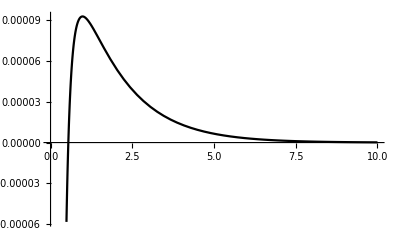

```mathematica
Plot[{lambda[r]},{r,0,10}]
```

```mathematica
ProjectionCoefficient[f1_,m1_,f2_,m2_,s_,ms_,i_,mi_,s1_,i1_,s2_,i2_]:= (-1)^(2i2-2s1-m1-m2-ms-mi)√((2f1+1)(2f2+1)(2s+1)(2i+1)) Sum[ThreeJSymbol[{s1,ms1},{i1,mi1},{f1, -m1}]*ThreeJSymbol[{s2,ms2},{i2,mi2},{f2,-m2}]*ThreeJSymbol[{s1,ms1},{s2,ms2},{s,-ms}]*ThreeJSymbol[{i1,mi1},{i2,mi2},{i,-mi}],{ms1,-s1,s1},{mi1,-i1,i1},{ms2,-s2,s2},{mi2,-i2,i2}];

SpinSpinMatrixElement[f1_,m1_,f1p_,m1p_,f2_,m2_,f2p_,m2p_,s1_,i1_,s2_,i2_]:= Sum[Sum[ProjectionCoefficient[f1,m1,f2,m2,s,ms,i,mi,s1,i1,s2,i2]*ProjectionCoefficient[f1p,m1p,f2p,m2p,s,ms,i,mi,s1,i1,s2,i2]*(3 ms^2-s(s+1)),{ms,-s,s},{mi,-i,i}],{s,Abs[s1-s2],Abs[s1+s2]},{i,Abs[i1-i2],Abs[i1+i2]}];
```

```mathematica
SpinSpinInteraction[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,3]]] KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[j,4]]])(1+KroneckerDelta[Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,3]]] KroneckerDelta[Rb87MF2basis[[jp,2]],Rb87MF2basis[[jp,4]]]))))*(SpinSpinMatrixElement[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87s,Rb87i,Rb87s,Rb87i]+SpinSpinMatrixElement[Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87MF2basis[[j,1]],Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87s,Rb87i,Rb87s,Rb87i]+ (-1)^p(-1)^l SpinSpinMatrixElement[Rb87MF2basis[[j,1]],MF2basis[[j,2]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87s,Rb87i,Rb87s,Rb87i]+ (-1)^p(-1)^l SpinSpinMatrixElement[Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87MF2basis[[j,1]],Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87s,Rb87i,Rb87s,Rb87i]),{j,1,5},{jp,1,5}]
```

```mathematica
(*Rb87SpinSpin=FullSimplify[ SpinSpinInteraction[0,0]];*)
```

```mathematica
(*MatrixForm[Rb87SpinSpin]*)
```

(1/4 | -(√(3/2))/2 | -(√3)/4 | (√3)/4 | 3/4
-(√(3/2))/2 | 1/2 | -1/(2 √2) | 1/(2 √2) | (√(3/2))/2
-(√3)/4 | -1/(2 √2) | 0 | 1 | (√3)/4
(√3)/4 | 1/(2 √2) | 1 | 0 | -(√3)/4
3/4 | (√(3/2))/2 | (√3)/4 | -(√3)/4 | 1/4)

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-3/2},{1,-1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-1/2},{1,-1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

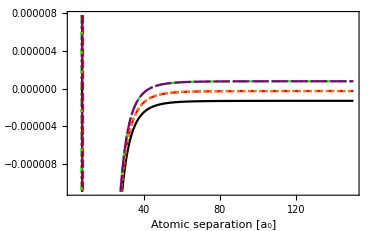

```mathematica
HZRb87[B_]=FullSimplify[HZsym[0,0,B]];
Htotal[r_,B_]= HZRb87[B]+Rb87TripletProjection*TripletNew[r]+Rb87SingletProjection*SingletNew[r];
Plot[{ Htotal[r, 0][[1, 1]], Htotal[r, 0][[2, 2]],Htotal[r, 0][[3, 3]],Htotal[r, 0][[4, 4]],Htotal[r, 0][[5, 5]]},{r,3,150},Frame->True,ImageSize->Large,FrameLabel->{"Atomic separation [a_0]","Energy [Hartree]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple}]
```

```mathematica
(C6*invcminHartree*AngstrominBohr^6)
(C8*invcminHartree*AngstrominBohr^8)
(C10*invcminHartree*AngstrominBohr^10)
```

4710.22

576696.

7.59128×10^7

```mathematica
βRb87 = β/.Solve[(-C6*AngstrominBohr^6*invcminHartree)/β^6-(C8*AngstrominBohr^8*invcminHartree)/β^8-(C10*AngstrominBohr^10*invcminHartree)/β^10==-1/(2 μRb87 β^2),β][[8]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

165.464

```mathematica
BohrinRb87vdw = 1/165.46400338488206
Rb87vdwinHartree = 1/(2 μRb87 βRb87^2);
HartreeinRb87vdw = 1/Rb87vdwinHartree
```

0.00604361

4.33744×10^9

```mathematica
C6vdw = (2 μRb87)/βRb87^4(C6*invcminHartree*AngstrominBohr^6)
C8vdw = (2 μRb87)/βRb87^6(C8*invcminHartree*AngstrominBohr^8)
C10vdw = (2 μRb87)/βRb87^8(C10*invcminHartree*AngstrominBohr^10)
C26vdw = (2 μRb87)/βRb87^24(C26*invcminHartree*AngstrominBohr^26)
```

0.995527

0.00445197

0.0000214049

1.76258×10^-21

```mathematica
μbvdw = μbH*HartreeinRb87vdw;
μnvdw = μnH*HartreeinRb87vdw;
```

```mathematica
TripletVDWdat= Table[{TripletNewdat[[i,1]]*BohrinRb87vdw, TripletNewdat[[i,2]]*HartreeinRb87vdw},{i,1,Length[TripletNewdat]}];
TripletVDW= Interpolation[TripletVDWdat];
SingletVDWdat= Table[{SingletNewdat[[i,1]]*BohrinRb87vdw, SingletNewdat[[i,2]]*HartreeinRb87vdw},{i,1,Length[SingletNewdat]}];
SingletVDW= Interpolation[SingletVDWdat];
```

```mathematica
Rb87vlr[r_]:= -C6vdw/r^6-C8vdw/r^8-C10vdw/r^10;
```

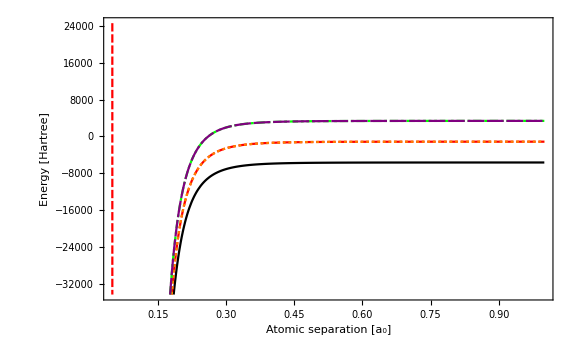

```mathematica
Plot[{ Htotal[r βRb87, 0][[1, 1]]HartreeinRb87vdw, Htotal[r βRb87, 0][[2, 2]]HartreeinRb87vdw,Htotal[r βRb87, 0][[3, 3]]HartreeinRb87vdw,Htotal[r βRb87, 0][[4, 4]]HartreeinRb87vdw,Htotal[r βRb87, 0][[5, 5]]HartreeinRb87vdw},{r,0.05,1.0},Frame->True,ImageSize->Large,FrameLabel->{"Atomic separation [a_0]","Energy [Hartree]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple}]
```

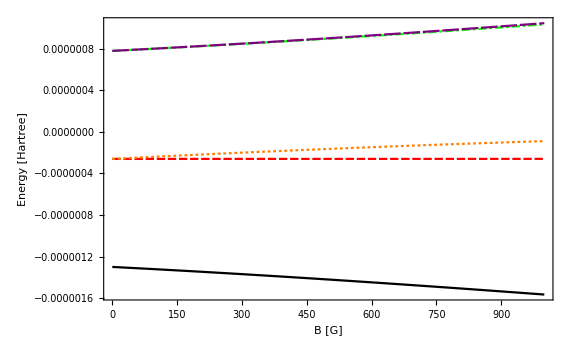

```mathematica
EigenSystemRb87[B_]:= Sort[Transpose[Eigensystem[HZRb87[B]]]];
Plot[{EigenSystemRb87[B][[1]][[1]],EigenSystemRb87[B][[2]][[1]],EigenSystemRb87[B][[3]][[1]],EigenSystemRb87[B][[4]][[1]],EigenSystemRb87[B][[5]][[1]]},{B,0,1000},ImageSize->Large,Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple}]
```

```mathematica
Aexvdw=Aex(AngstrominBohr BohrinRb87vdw)^-gamma
```

2.80813×10^14

```mathematica
Rb87vlrNew[r_]:= -C6vdw/r^6-C8vdw/r^8-C10vdw/r^10-( Aexvdw r^gamma) Exp[-beta /(AngstrominBohr BohrinRb87vdw)*r]*invcminHartree*HartreeinRb87vdw ;
```

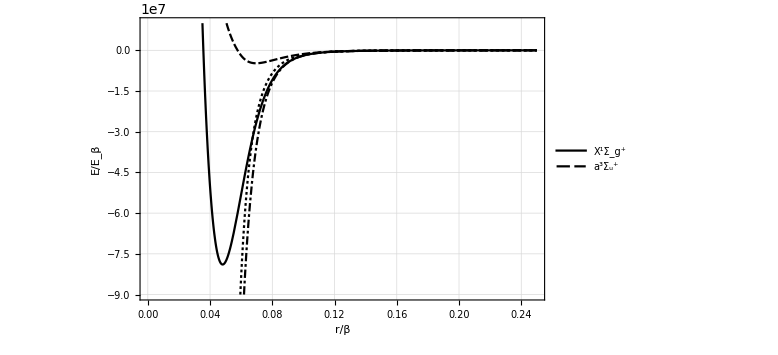

```mathematica
Plot[{SingletVDW[r],TripletVDW[r],Rb87vlr[r],Rb87vlrNew[r](*-C26vdw/r^26*)},{r,0.02,0.25},PlotRange->{-9.0*10^7,10^7},ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"r/β","E/E_β"},LabelStyle->Medium,PlotLegends->{"X^1Σ_g^+","a^3Σ_u^+"}]
```

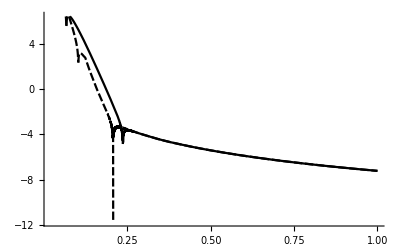

```mathematica
Plot[{Log[10,Abs[(SingletVDW[r]-Rb87vlr[r])]],Log[10,Abs[(SingletVDW[r]-Rb87vlrNew[r])]]},{r,0.02,1}]
```

```mathematica
Rb87Avdw=Rb87AH*HartreeinRb87vdw;
Rb87HZVDW[p_,l_,B_]:=
Table[(1/(√((1+KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,3]]] KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[j,4]]])(1+KroneckerDelta[Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,3]]] KroneckerDelta[Rb87MF2basis[[jp,2]],Rb87MF2basis[[jp,4]]]))))*(HZ[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87Avdw,B,μbvdw]KroneckerDelta[Rb87MF2basis[[j,3]],Rb87MF2basis[[jp,3]]]KroneckerDelta[Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,4]]]+HZ[Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87Avdw,B,μbvdw]KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[jp,1]]]KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87Avdw,B,μbvdw]KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[jp,3]]]KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87Avdw,B,μbvdw]KroneckerDelta[Rb87MF2basis[[j,3]],Rb87MF2basis[[jp,1]]]KroneckerDelta[Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,2]]]),{j,1,Length[Rb87MF2basis]},{jp,1,Length[Rb87MF2basis]}];
```

```mathematica
Rb87HZ[B_]=FullSimplify[Rb87HZVDW[0,0,B]];
```

```mathematica
Rb87HVDW[r_,B_]=Rb87HZ[B]+Rb87TripletProjection*TripletVDW[r]+Rb87SingletProjection*SingletVDW[r];
Rb87Eigensystem[B_]:= Sort[Transpose[Eigensystem[Rb87HZ[B]]]];
```

```mathematica
DD[B_]:= Transpose[{Rb87Eigensystem[B][[1]][[2]],Rb87Eigensystem[B][[2]][[2]],Rb87Eigensystem[B][[3]][[2]],Rb87Eigensystem[B][[4]][[2]],Rb87Eigensystem[B][[5]][[2]]}];
Rb87Eth[B_]:= Table[Rb87Eigensystem[B][[j]][[1]],{j,1,5}];
```

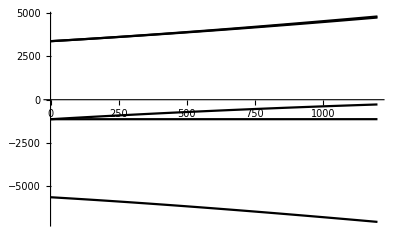

```mathematica
Plot[Rb87Eth[B],{B,0,1200}]
```

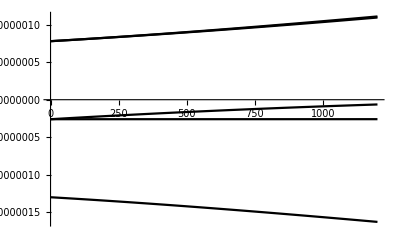

```mathematica
Plot[Rb87Eth[B]*1/HartreeinRb87vdw,{B,0,1200}]
```

```mathematica
RGridvdw=Table[r,{r,0.05,5.0,0.001}];NR=Length[RGridvdw]
```

4951

```mathematica
ValVecs[B_]:=Table[ Sort[Transpose[Eigensystem[Rb87HVDW[RGridvdw[[iR]],B]]]],{iR,1,NR}];
```

```mathematica
AdiabaticUV[B_]:=Module[{ValVecsLocal,diagpots},
ValVecsLocal=ValVecs[B];
diagpots=Table[{{RGridvdw[[iR]],ValVecsLocal[[iR,n,1]]},ValVecsLocal[[iR,n,2]]},{iR,1,NR,1},{n,1,5}];
diagpots
]
```

```mathematica
AUV=AdiabaticUV[Btest];Adiabaticpots=Table[AUV[[1;;Length[AUV],n,1]],{n,1,5}];
```

```mathematica
AdiabaticInterpPots=Table[Interpolation[AUV[[1;;Length[AUV],n,1]]],{n,1,5}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

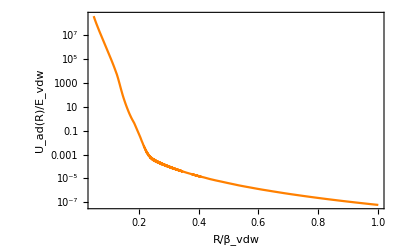

```mathematica
ntest=4;padiabatic=LogPlot[Abs[AdiabaticInterpPots[[ntest]][r]-Rb87Eth[Btest][[ntest]]-Rb87vlr[r] ],{r,0.05,1.0},Frame->True,PlotStyle->{Black,Red,Blue,Green,Orange},FrameLabel->{"R/β_vdw","U_ad(R)/E_vdw"}]
```

Okay, can we make this agreement any better in the region near 0.2 ?

```mathematica
(*Rb87vlr[r_]:=AdiabaticInterpPots[[1]][r]-Rb87Eth[Btest][[1]] *)
```

```mathematica
35/βRb87
```

0.211526

```mathematica
χminus[r_,l_]:= Sqrt[r] BesselJ[1/4(2l+1),1/(2 r^2) ];
χmprime[r_,l_]:= D[χminus[rp,l],rp]/.rp->r;
f[l_,k_,r_]:=r SphericalBesselJ[l,k r];
g[l_,k_,r_]:= r SphericalBesselY[l,k r];
dfdr[l_,k_,r_]:=D[f[l,k,rp],rp]/.rp->r; 
dgdr[l_,k_,r_]:=D[g[l,k,rp],rp]/. rp->r; 
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=α';
g0=- α[r]Cos[ϕ+phaseint[r]];
f0= α[r]Sin[ϕ+phaseint[r]];
f0p=αp[r]/α[r] f0-1/α[r]^2 g0;
g0p=αp[r]/α[r] g0+1/α[r]^2 f0;
χm=χminus[r,l];
χmp=χmprime[r,l];
{f0,g0,f0p,g0p,χm,χmp}]
```

```mathematica
4 βRb87
```

661.856

```mathematica
45/βRb87
```

0.271962

```mathematica
rx = 0.1;
rf = 7.0;(*300*BohrinRb87vdw;*)
r0 =35/βRb87;(* 30*BohrinRb87vdw;*)
rmin = 1.0*BohrinRb87vdw;
rmax = r0;
ltest = 0;
Etest = 10^-16; 
ksqr[Ε_,l_,r_]:=(Ε - Rb87vlr[r]-(l(l+1))/r^2);
BC1[Ε_,l_,r_,rx_]:=1/Sqrt[(Ε - Rb87vlr[r]-(l(l+1))/r^2)^(1/2)]/.r->rx;
BC2[Ε_,l_,r_,rx_]:=D[1/Sqrt[(Ε - Rb87vlr[r]-(l(l+1))/r^2)^(1/2)],r]/.r->rx;
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqr[Etest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[Etest,ltest,r,rx],α'[rx]==BC2[Etest,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,2}]];
α0fun=Table[α/.α0sol[[i]],{i,1,Length[α0sol]}];
nr=300;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,2}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,2}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,2}],{rf,rGrid}]];
ϕRb87=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}];
```

```mathematica
ϕRb87[[1]]
```

1.1084

```mathematica
CalcQuantumDefect[Ε_,l_,rmin_,rmax_,r0_,rx_,rf_,r_,nr_,U_,ϕ_]:= Module[{phaseint,αp,rp,αfun,α,f0,f0p,g0,g0p,u,up,Y,Ksr,mu},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,r0}];
αp=αfun';
f0=α[r0]Sin[ϕ+phaseint];
g0=-α[r0]Cos[ϕ+phaseint];
g0p=αp[r0]/αfun[r0] g0+1/αfun[r0]^2 f0;
f0p=αp[r0]/αfun[r0] f0-1/αfun[r0]^2 g0;
u=NDSolveValue[{-u''[r]+ (U[r]+(l(l+1))/r^2)u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax},AccuracyGoal->8];
up=u';
Y = up[r]/u[r]/.r->r0;
Ksr = (Y f0 -f0p)/(Y g0 -g0p);
mu = 1/π ArcTan[Ksr];
Return[mu]
]
```

```mathematica
Rb87SingletQD=CalcQuantumDefect[Etest,0,rmin,rmax,r0,rx,rf,r,nr,SingletVDW,ϕRb87[[1]]]
```

-0.0441526

```mathematica
Rb87TripletQD=CalcQuantumDefect[Etest,0,rmin,rmax,r0,rx,rf,r,nr,TripletVDW,ϕRb87[[1]]]
```

-0.0787846

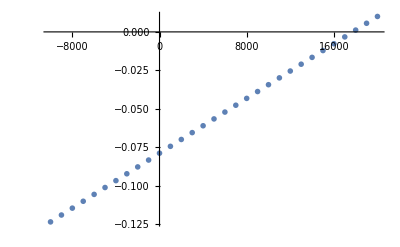

```mathematica
ListPlot[Table[{Etest, CalcQuantumDefect[Etest,0,rmin,rmax,r0,rx,rf,r,nr,TripletVDW,ϕRb87[[1]]]},{Etest,-10000,20000,1000}]]
```

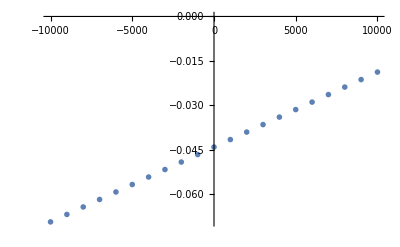

```mathematica
ListPlot[Table[{Etest, CalcQuantumDefect[Etest,0,rmin,rmax,r0,rx,rf,r,nr,SingletVDW,ϕRb87[[1]]]},{Etest,-10000,10000,1000}]]
```

```mathematica
KsrFTEI[B_]:= Transpose[DD[B]].(Rb87SingletProjection*Tan[π Rb87SingletQD]+Rb87TripletProjection*Tan[π Rb87TripletQD 1.1]).DD[B]
```

```mathematica
MatrixForm[KsrFTEI[1000]]
```

(-0.262601 | -0.0246459 | 0.0282571 | 0.0189604 | -0.0165913
-0.0246459 | -0.242582 | -0.0419752 | -0.0281652 | 0.0246459
0.0282571 | -0.0419752 | -0.231067 | 0.032292 | -0.0282571
0.0189604 | -0.0281652 | 0.032292 | -0.257525 | -0.0189604
-0.0165913 | 0.0246459 | -0.0282571 | -0.0189604 | -0.262601)

```mathematica
KsrFTEIPP[B_]:= KsrFTEI[B][[1,1]];
KsrFTEIQP[B_]:=KsrFTEI[B][[2;;5,1]];
KsrFTEIPQ[B_]:=KsrFTEI[B][[1,2;;5]];
KsrFTEIQQ[B_]:=KsrFTEI[B][[2;;5,2;;5]];
```

```mathematica
En=500;
Emin = 10^-16;
Emax =15000;
EGrid=Table[Emin+((i-1)/(En-1))^3(Emax-Emin),{i,1,En}];
```

```mathematica
calcTanGamma[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{αfun,phaseint,g0,g0p,f0,f0p,αp,α,κ,rp,gbound,gboundp,tanγ},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
κ=√-Ε;
gbound=√(κ/π rp) BesselK[l+1/2,κ rp]/.rp->rf;
gboundp=D[√(κ/π rp) BesselK[l+1/2,κ rp],rp]/.rp->rf;
tanγ =-(gbound g0p-gboundp g0)/(gbound f0p - gboundp f0);
Return[tanγ]
]
```

```mathematica
gammaTable=Table[{-EGrid[[ii]],ArcTan[calcTanGamma[0,rx,rf,r,-EGrid[[ii]],ϕRb87[[1]]]]},{ii,1,Length[EGrid]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

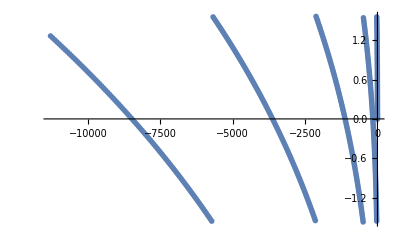

```mathematica
ListPlot[gammaTable,PlotRange->Full]
```

```mathematica
GammaTablenew=gammaTable;
For[i=1,i<Length[gammaTable],i++,
If[(gammaTable[[i+1,2]]-gammaTable[[i,2]]<-1.2),Print[i];
GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]+π,GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]]
]
```

60

160

261

362

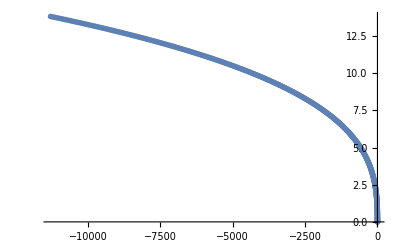

```mathematica
ListPlot[GammaTablenew]
```

```mathematica
Gammafun = Interpolation[GammaTablenew(*,InterpolationOrder->1*)];
```

```mathematica
Gammafun[0]
```

5.67813×10^-6

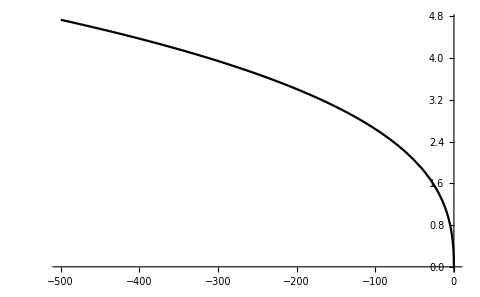

```mathematica
Plot[{Gammafun[ϵ],1/2 abar√(-ϵ)},{ϵ,-500,0},PlotStyle->{Black,Red}]
```

```mathematica
CotGamma2[B_,Ε_]:= Cot[Gammafun[((Rb87Eth[B][[1]]+Ε)-Rb87Eth[B][[2]])]];
CotGamma3[B_,Ε_]:= Cot[Gammafun[((Rb87Eth[B][[1]]+Ε)-Rb87Eth[B][[3]])]];
CotGamma4[B_,Ε_]:= Cot[Gammafun[((Rb87Eth[B][[1]]+Ε)-Rb87Eth[B][[4]])]];
CotGamma5[B_,Ε_]:= Cot[Gammafun[((Rb87Eth[B][[1]]+Ε)-Rb87Eth[B][[5]])]];
CotGammaMatrix[B_,Ε_]:=DiagonalMatrix[{CotGamma2[B,Ε],CotGamma3[B,Ε],CotGamma4[B,Ε],CotGamma5[B,Ε]}];
```

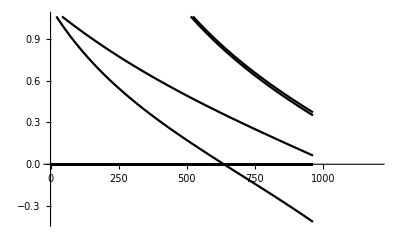

```mathematica
Plot[CotGammaMatrix[Btest,Etest],{Btest,0,1200}]
```

```mathematica
bmax = 1400;
bmin = 0;
bn = 500;
bgrid = Table[(bmax-bmin)/bn i,{i,0,bn}];
Etest = 10^-2;
KtildeFTEI[B_,Ε_]:= KsrFTEIPP[B]-KsrFTEIPQ[B].Inverse[KsrFTEIQQ[B]+CotGammaMatrix[B,Ε]].KsrFTEIQP[B];
```

DiagonalMatrix::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of DiagonalMatrix::mindet will be suppressed during this calculation.

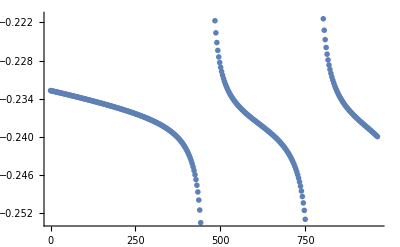

```mathematica
ListPlot[{Table[{bgrid[[ii]],KtildeFTEI[bgrid[[ii]],Etest]},{ii,1,bn+1}]}]
```

```mathematica
CalcTanEta[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,gs,fs,fsp,gsp,k,tanη,αfun,phaseint,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs =g[l,k,r];
gsp=dgdr[l,k,r];
tanη=(fs f0p-f0 fsp)/(gs f0p-f0 gsp)/.r->rf;
Return[tanη]
]
```

```mathematica
EtaTable=Table[{EGrid2[[ii]],ArcTan[CalcTanEta[ltest,rx,rf,r,EGrid2[[ii]],ϕRb87[[1]]]]},{ii,1,Length[EGrid2]}];
```

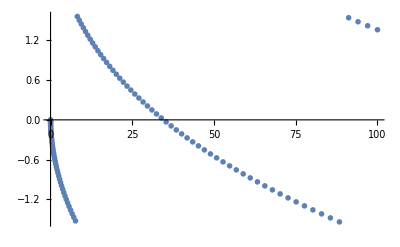

```mathematica
ListPlot[EtaTable]
```

```mathematica
EtaTablenew2=EtaTable;
For[i=1,i<Length[EtaTable],i++,
If[(EtaTable[[i+1,2]]-EtaTable[[i,2]]>1.2),Print[i];
EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]-π,EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]]
]
```

43

96

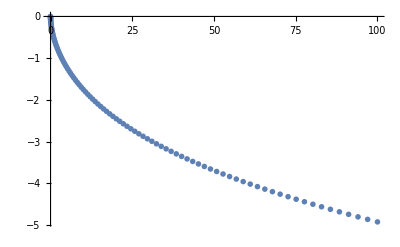

```mathematica
ListPlot[EtaTablenew2]
```

```mathematica
Etafun=Interpolation[EtaTablenew2,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Etafun[0]
```

-4.82364×10^-9

```mathematica
CalcA[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,fs,fsp,gs,gsp,k,A,αfun,phaseint,α,αp,tanη,Wfsf0,Wgsf0,Wfsg0,Wgsg0},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
f0=αfun[rf]Sin[ϕ+phaseint];
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,rf];
fsp=dfdr[l,k,rf];
gs=g[l,k,rf];
gsp=dgdr[l,k,rf];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
A=-((Wfsg0 -tanη Wgsg0)/(Wgsf0+tanη Wfsf0));
Return[A]
]
```

```mathematica
En2=100;
Emin2 = 10^-16;
Emax2=100;
EGrid2=Table[Emin2+((i-1)/(En2-1))^3(Emax2-Emin2),{i,1,En2}];
```

```mathematica
ATable=Table[{EGrid2[[ii]],CalcA[ltest,rx,rf,r,EGrid2[[ii]],ϕRb87[[1]]]},{ii,1,Length[EGrid2]}];
```

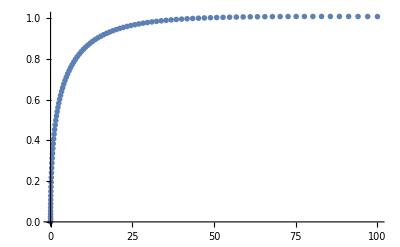

```mathematica
ListPlot[ATable]
```

```mathematica
Afun = Interpolation[ATable,InterpolationOrder->1]
```

InterpolatingFunction[…]

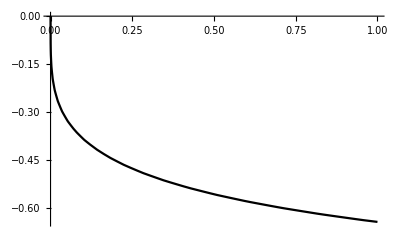

```mathematica
Plot[-Sqrt[Afun[ϵ]],{ϵ,0,1},PlotRange->{0,-1}]
```

```mathematica
Afun[0]
```

4.76044×10^-9

```mathematica
CalcG[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,k,tanη,G,fs,fsp,gs,gsp,αfun,phaseint,Wfsf0,Wgsf0,Wfsg0,Wgsg0,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
f0=αfun[rf]Sin[ϕ+phaseint];
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[ Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs=g[l,k,r];
gsp=dgdr[l,k,r];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
G=-(Wfsg0*Wfsf0+Wgsg0*Wgsf0)/(Wfsf0^2+Wgsf0^2)/.r->rf;
(*G =-((g0 gsp-g0p gs)+tanη(g0 fsp-g0p fs))/((f0 gsp - f0p gs)+tanη (f0 fsp - f0p fs))/.r->rf;*)
Return[G]
]
```

```mathematica
GTable=Table[{EGrid2[[ii]],CalcG[ltest,rx,rf,r,EGrid2[[ii]],ϕRb87[[1]]]},{ii,1,Length[EGrid2]}];
```

```mathematica
Gfun =Interpolation[GTable,InterpolationOrder->1];
```

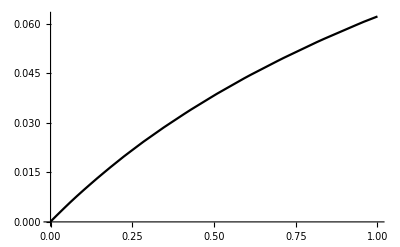

```mathematica
Plot[Gfun[x],{x,0,1.0}]
```

```mathematica
Gfun[0]
```

0.0000841663

```mathematica
Etest =10^-3;
KFTEITable = Table[{bgrid[[ii]], Sqrt[Afun[Etest]] (KtildeFTEI[bgrid[[ii]],Etest]^-1+Gfun[Etest])^-1 Sqrt[Afun[Etest]]},{ii,1,bn+1}];
```

DiagonalMatrix::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of DiagonalMatrix::mindet will be suppressed during this calculation.

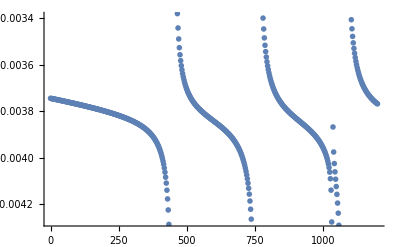

```mathematica
ListPlot[{KFTEITable}]
```

```mathematica
KFTEIfun[B_,Etest_]:= Sqrt[Afun[Etest]](KtildeFTEI[B,Etest]^-1+Gfun[Etest])^-1 Sqrt[Afun[Etest]];
```

```mathematica
Sfun[B_,Etest_]:= Exp[ⅈ Etafun[Etest]] ((1+ⅈ KFTEIfun[B,Etest])/(1-ⅈ KFTEIfun[B,Etest])) Exp[ⅈ Etafun[Etest]];
ascatfun[B_,Etest_]:= -1/(ⅈ Sqrt[Etest]) ((Sfun[B,Etest]-1)/(Sfun[B,Etest]+1));
```

```mathematica
(*KFTEIfunNew[B_,Etest_]:= AOneHalfC6[Etest](KtildeFTEI[B,Etest]^-1+GC6[Etest])^-1 AOneHalfC6[Etest];
SfunNew[B_,Etest_]:= Exp[ⅈ EtaC6[Etest]] ((1+ⅈ KFTEIfunNew[B,Etest])/(1-ⅈ KFTEIfunNew[B,Etest])) Exp[ⅈ EtaC6[Etest]];
ascatfunNew[B_,Etest_]:= -1/(ⅈ Sqrt[Etest]) ((SfunNew[B,Etest]-1)/(SfunNew[B,Etest]+1));*)
```

```mathematica
cotdeltafun[Ε_,B_]:=(1-Tan[Etafun[Ε]]KFTEIfun[B,Ε])/(Tan[Etafun[Ε]]+KFTEIfun[B,Ε]);
```

```mathematica
CalcERE[ΕMin_,ΕMax_,Btest_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{ Εtest,√Εtest cotdeltafun[Εtest,Btest]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
mqdtresdat =Table[{B, CalcERE[10^-5,10^-2,B][[1]]},{B,0,1200,1}];
```

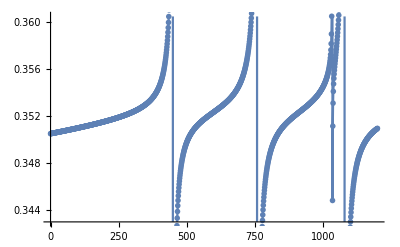

```mathematica
ListPlot[mqdtresdat,Joined->True]
```

```mathematica
abar[L_]:=((π 2^(-(2L+3/2)))/(Gamma[L/2+5/4]Gamma[L+1/2]))^(2/(2L+1))
```

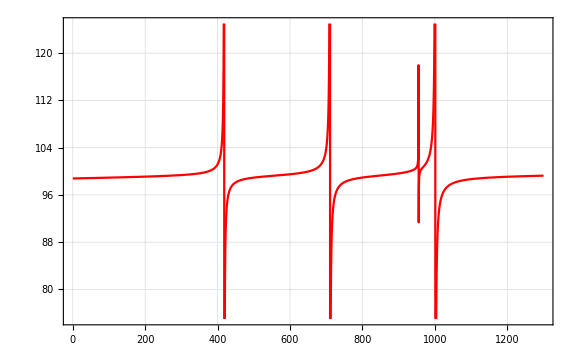

```mathematica
p15= Plot[{ascatfun[B,10^-2]*1/BohrinRb87vdw(*,ascatfunNew[B,10^-2]*1/BohrinRb87vdw*)},{B,0,1300},Frame->True,GridLines->Automatic,ImageSize->Large,PlotRange->{75,125},PlotStyle->{Red}]
```

```mathematica
(*Show[p6,p7,p8,p9,p10]*)
```

Blue (rx = 0.065 vdw, rf = 300 bohr, rm = 30 bohr); Red (rx = 0.065 vdw, rf = 500 bohr, rm = 30 bohr); Black (rx = 0.065 vdw, rf = 1000 bohr, rm = 30 bohr);  Green (rx = 0.065 vdw, rf = 1000 bohr, rm = 45 bohr); Gray (rx = 0.065 vdw, rf = 300 bohr, rm = 25 bohr)

```mathematica
(*Show[p6,p14,p15]*)
```

Blue (rx = 0.065 vdw, rf = 300 bohr, rm = 30 bohr); Purple (rx = 0.10 vdw, rf = 300 bohr, rm = 30 bohr); Red (rx = 0.075; rf = 300 bohr; rm = 30 bohr)

```mathematica
logderdat = Import["/Users/niravmehta/Documents/GitHub/LiScattering/Rb87FR.dat"];
```

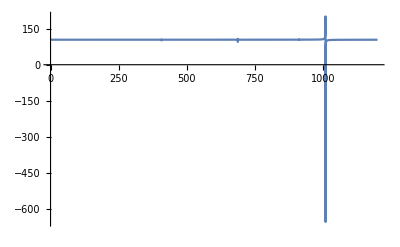

```mathematica
p3 =ListPlot[logderdat,Joined->True,PlotMarkers->None,PlotRange->All]
```

```mathematica
sigma=4π (Transpose[logderdat][[2]])^2;
```

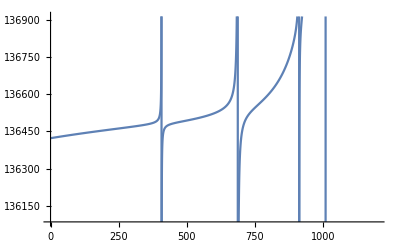

```mathematica
psigmaExact=ListPlot[Transpose[{Transpose[logderdat][[1]],sigma}],Joined->True,PlotMarkers->None]
```

```mathematica
KsrFTEI[B_]:= Transpose[DD[B]].(Rb87SingletProjection*Tan[π Rb87SingletQD ]+Rb87TripletProjection*Tan[π Rb87TripletQD ]).DD[B];
KtildeFTEI[B_,Ε_]:= KsrFTEIPP[B]-KsrFTEIPQ[B].Inverse[KsrFTEIQQ[B]+CotGammaMatrix[B,Ε]].KsrFTEIQP[B];
```

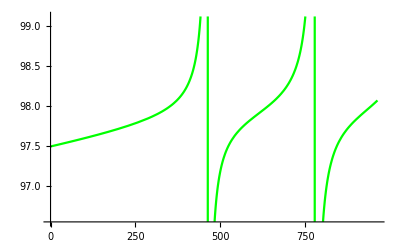

```mathematica
pftnew=Plot[{(βRb87 abar[0](1-KtildeFTEI[B,10^-14]))},{B,0,1400},PlotStyle->{Black,Red,Green},PlotRange->Automatic]
```

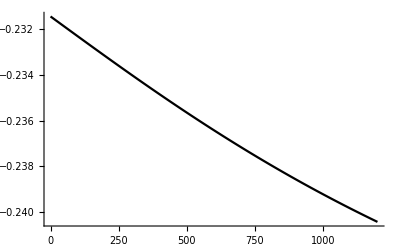

```mathematica
Plot[KsrFTEIPP[B],{B,0,1200}]
```

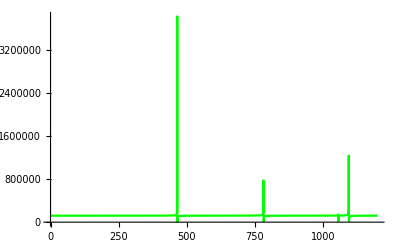

```mathematica
pftsigmanew=Plot[{ 4π (βRb87 abar[0](1-KtildeFTEI[B,10^-14]))^2},{B,0,1200},PlotStyle->{Black,Red,Green},PlotRange->All]
```

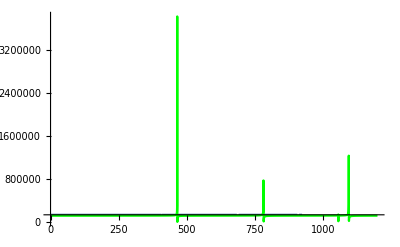

```mathematica
Show[psigmaExact,pftsigmanew,PlotRange->Automatic]
```

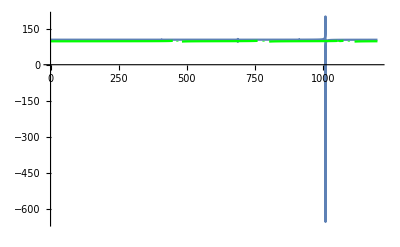

```mathematica
Show[p3,pftnew]
```

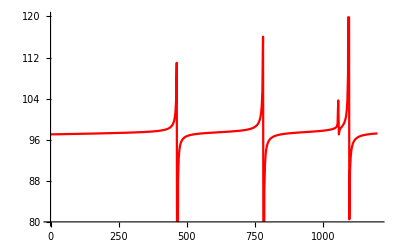

```mathematica
p4=ListPlot[Table[{bgrid[[i]],ascatfun[bgrid[[i]],0.01]*1/BohrinRb87vdw},{i,1,bn+1}],PlotStyle->Red,PlotRange->{80,120},Joined->True,PlotMarkers->None]
```

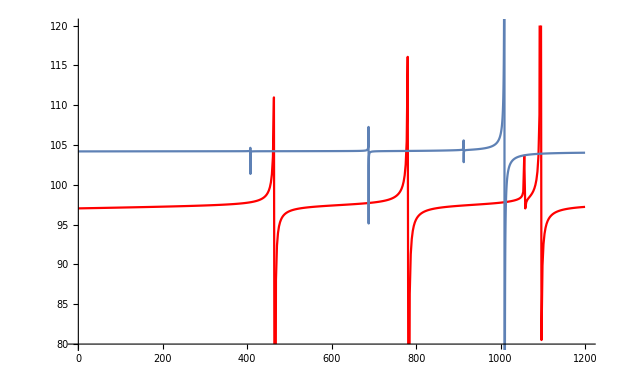

```mathematica
Show[p4,p3]
```

### Read in the log-derivative matrix to find K_sr

```mathematica
RunProcess["/Users/niravmehta/Documents/GitHub/LiScattering/Rb-LogDerMat.x"]
```

<|ExitCode→0,StandardOutput→ size of the Rb-87 1-atom hyperfine basis =            8
 1-atom Rb-87 states:
   2  -2
   2   0
   2   2
   4  -4
   4  -2
   4   0
   4   2
   4   4
 CGhf =    0.0000000000000000     
 setting up potentials
 zerostate =            0           0           0           0
Generating the unsymmetrized basis with total MF =   4
    #   f1   m1   f2   m2
  ---  ---  ---  ---  ---
    1    2    0    4    4
    2    2    2    2    2
    3    2    2    4    2
    4    4    0    4    4
    5    4    2    2    2
    6    4    2    4    2
    7    4    4    2    0
    8    4    4    4    0
(+1/0/-1) = (boson/dist/fermion) Symmetry case:  1
partial wave =  0
   1  symmetrized basis: 0.71 ( | 2 0 4 4> +  1| 4 4 2 0> )
   2  symmetrized basis: 0.50 ( | 2 2 2 2> +  1| 2 2 2 2> )
   3  symmetrized basis: 0.71 ( | 2 2 4 2> +  1| 4 2 2 2> )
   4  symmetrized basis: 0.71 ( | 4 0 4 4> +  1| 4 4 4 0> )
   5  symmetrized basis: 0.50 ( | 4 2 4 2> +  1| 4 2 4 2> )
 size of the symmetrized 2-atom hyperfine basis =            5
 The singlet projection matrix:
 -------------------------------
        0.2500000000       -0.2165063509       -0.1767766953       -0.2500000000        0.2165063509
       -0.2165063509        0.1875000000        0.1530931089        0.2165063509       -0.1875000000
       -0.1767766953        0.1530931089        0.1250000000        0.1767766953       -0.1530931089
       -0.2500000000        0.2165063509        0.1767766953        0.2500000000       -0.2165063509
        0.2165063509       -0.1875000000       -0.1530931089       -0.2165063509        0.1875000000
 The triplet projection matrix:
 -------------------------------
        0.7500000000        0.2165063509        0.1767766953        0.2500000000       -0.2165063509
        0.2165063509        0.8125000000       -0.1530931089       -0.2165063509        0.1875000000
        0.1767766953       -0.1530931089        0.8750000000       -0.1767766953        0.1530931089
        0.2500000000       -0.2165063509       -0.1767766953        0.7500000000        0.2165063509
       -0.2165063509        0.1875000000        0.1530931089        0.2165063509        0.8125000000
 Energy =   -2.5436359701814056E-006 B-field =    0.0000000000000000      yf = 
       -0.1283578181        0.0040041935        0.0000000000        0.0016405745        0.0000000000
        0.0040041935        0.4094894614       -0.0000000001       -0.0022868079       -0.0000000000
        0.0000000000       -0.0000000001        0.4188713968       -0.0000000000        0.0000000000
        0.0016405745       -0.0022868079       -0.0000000000        0.5383855420       -0.0000000000
        0.0000000000       -0.0000000000        0.0000000000       -0.0000000000        0.5388663603
 Energy =   -2.5680295145063647E-006 B-field =    111.11111111111111      yf = 
       -0.1280884801       -0.0023742544       -0.0036288825       -0.0010673055       -0.0009239997
       -0.0023742544        0.4257779699       -0.0058603619       -0.0010021812       -0.0008675668
       -0.0036288825       -0.0058603619        0.4323389748       -0.0014826138       -0.0012834660
       -0.0010673055       -0.0010021812       -0.0014826138        0.5467043781       -0.0001883670
       -0.0009239997       -0.0008675668       -0.0012834660       -0.0001883670        0.5468000028
 Energy =   -2.5939300155034467E-006 B-field =    222.22222222222223      yf = 
       -0.1278322303        0.0024119485       -0.0041937867       -0.0009130002       -0.0007901916
        0.0024119486        0.4375396905        0.0081895208        0.0010042327        0.0008689467
       -0.0041937867        0.0081895208        0.4566858295       -0.0016285989       -0.0014091931
       -0.0009130002        0.0010042327       -0.0016285989        0.5550204271       -0.0001471164
       -0.0007901916        0.0008689467       -0.0014091931       -0.0001471164        0.5552124648
 Energy =   -2.6212324121115431E-006 B-field =    333.33333333333337      yf = 
       -0.1275797728        0.0023963746       -0.0051872229       -0.0007719979       -0.0006680397
        0.0023963746        0.4518186094        0.0124866865        0.0009976115        0.0008628201
       -0.0051872229        0.0124866865        0.4909217166       -0.0019238598       -0.0016638897
       -0.0007719979        0.0009976115       -0.0019238598        0.5635166514       -0.0001115845
       -0.0006680397        0.0008628201       -0.0016638897       -0.0001115845        0.5638541737
 Energy =   -2.6498362644467407E-006 B-field =    444.44444444444446      yf = 
       -0.1272996107       -0.0022007543        0.0073381750       -0.0006315991        0.0005467093
       -0.0022007543        0.4704116485        0.0224053215       -0.0009440793        0.0008164192
        0.0073381750        0.0224053215        0.5523595491        0.0026118366       -0.0022585615
       -0.0006315991       -0.0009440793        0.0026118366        0.5721741580        0.0000772614
        0.0005467093        0.0008164192       -0.0022585615        0.0000772614        0.5726888461
 Energy =   -2.6796463733842731E-006 B-field =    555.55555555555554      yf = 
       -0.1267964091        0.0008763724       -0.0152583753       -0.0004245352       -0.0003679651
        0.0008763724        0.5004664100        0.0617228177        0.0005341170        0.0004621216
       -0.0152583753        0.0617228177        0.7509163578       -0.0052336723       -0.0045275186
       -0.0004245352        0.0005341170       -0.0052336723        0.5809939061       -0.0000239993
       -0.0003679651        0.0004621216       -0.0045275186       -0.0000239993        0.5816987740
 Energy =   -2.7105731498801323E-006 B-field =    666.66666666666674      yf = 
       -0.1289264132        0.0134748092        0.0393151614       -0.0011030743       -0.0009561368
        0.0134748092        0.4682864090       -0.2263692564        0.0048124732        0.0041677779
        0.0393151614       -0.2263692564       -0.5428758077        0.0130154396        0.0112714839
       -0.0011030743        0.0048124732        0.0130154396        0.5896378589       -0.0002265939
       -0.0009561368        0.0041677779        0.0112714839       -0.0002265939        0.5906153824
 Energy =   -2.7425327810080564E-006 B-field =    777.77777777777783      yf = 
       -0.1274043474        0.0075874084        0.0065959394       -0.0005648279       -0.0004910707
        0.0075874084        0.5560629677       -0.0619933978        0.0029950695        0.0025989215
        0.0065959394       -0.0619933978        0.2449605054        0.0020874440        0.0018111522
       -0.0005648279        0.0029950695        0.0020874440        0.5987903639       -0.0000761504
       -0.0004910707        0.0025989215        0.0018111522       -0.0000761504        0.5999390901
 Energy =   -2.7754472367790543E-006 B-field =    888.88888888888891      yf = 
       -0.1270580187        0.0099059367        0.0025670818       -0.0004167874       -0.0003637487
        0.0099059367        0.6762742334       -0.0569696963        0.0041720430        0.0036305749
        0.0025670818       -0.0569696963        0.3431506773        0.0007100866        0.0006177824
       -0.0004167874        0.0041720430        0.0007100866        0.6078996668       -0.0000351856
       -0.0003637487        0.0036305749        0.0006177824       -0.0000351856        0.6092463606
 Energy =   -2.8092441569323946E-006 B-field =    1000.0000000000000      yf = 
       -0.1263104672        0.0304653429       -0.0014924132       -0.0000704150       -0.0000626567
        0.0304653429        1.4101644980       -0.1427096728        0.0138121399        0.0120660037
       -0.0014924132       -0.1427096728        0.3976376164       -0.0009831680       -0.0008589984
       -0.0000704150        0.0138121399       -0.0009831680        0.6171751456        0.0000922227
       -0.0000626567        0.0120660037       -0.0008589984        0.0000922227        0.6186875744
,StandardError→|>

```mathematica
logderoutput=Import["/Users/niravmehta/Documents/GitHub/LiScattering/logderdata.dat"]
```

{{0.},{-0.128358,0.00400419,0.,0.00164057,0.},{0.00400419,0.409489,-1.×10^-10,-0.00228681,0.},{0.,-1.×10^-10,0.418871,0.,0.},{0.00164057,-0.00228681,0.,0.538386,0.},{0.,0.,0.,0.,0.538866},{111.111},{-0.128088,-0.00237425,-0.00362888,-0.00106731,-0.000924},{-0.00237425,0.425778,-0.00586036,-0.00100218,-0.000867567},{-0.00362888,-0.00586036,0.432339,-0.00148261,-0.00128347},{-0.00106731,-0.00100218,-0.00148261,0.546704,-0.000188367},{-0.000924,-0.000867567,-0.00128347,-0.000188367,0.5468},{222.222},{-0.127832,0.00241195,-0.00419379,-0.000913,-0.000790192},{0.00241195,0.43754,0.00818952,0.00100423,0.000868947},{-0.00419379,0.00818952,0.456686,-0.0016286,-0.00140919},{-0.000913,0.00100423,-0.0016286,0.55502,-0.000147116},{-0.000790192,0.000868947,-0.00140919,-0.000147116,0.555212},{333.333},{-0.12758,0.00239637,-0.00518722,-0.000771998,-0.00066804},{0.00239637,0.451819,0.0124867,0.000997612,0.00086282},{-0.00518722,0.0124867,0.490922,-0.00192386,-0.00166389},{-0.000771998,0.000997612,-0.00192386,0.563517,-0.000111585},{-0.00066804,0.00086282,-0.00166389,-0.000111585,0.563854},{444.444},{-0.1273,-0.00220075,0.00733818,-0.000631599,0.000546709},{-0.00220075,0.470412,0.0224053,-0.000944079,0.000816419},{0.00733818,0.0224053,0.55236,0.00261184,-0.00225856},{-0.000631599,-0.000944079,0.00261184,0.572174,0.0000772614},{0.000546709,0.000816419,-0.00225856,0.0000772614,0.572689},{555.556},{-0.126796,0.000876372,-0.0152584,-0.000424535,-0.000367965},{0.000876372,0.500466,0.0617228,0.000534117,0.000462122},{-0.0152584,0.0617228,0.750916,-0.00523367,-0.00452752},{-0.000424535,0.000534117,-0.00523367,0.580994,-0.0000239993},{-0.000367965,0.000462122,-0.00452752,-0.0000239993,0.581699},{666.667},{-0.128926,0.0134748,0.0393152,-0.00110307,-0.000956137},{0.0134748,0.468286,-0.226369,0.00481247,0.00416778},{0.0393152,-0.226369,-0.542876,0.0130154,0.0112715},{-0.00110307,0.00481247,0.0130154,0.589638,-0.000226594},{-0.000956137,0.00416778,0.0112715,-0.000226594,0.590615},{777.778},{-0.127404,0.00758741,0.00659594,-0.000564828,-0.000491071},{0.00758741,0.556063,-0.0619934,0.00299507,0.00259892},{0.00659594,-0.0619934,0.244961,0.00208744,0.00181115},{-0.000564828,0.00299507,0.00208744,0.59879,-0.0000761504},{-0.000491071,0.00259892,0.00181115,-0.0000761504,0.599939},{888.889},{-0.127058,0.00990594,0.00256708,-0.000416787,-0.000363749},{0.00990594,0.676274,-0.0569697,0.00417204,0.00363057},{0.00256708,-0.0569697,0.343151,0.000710087,0.000617782},{-0.000416787,0.00417204,0.000710087,0.6079,-0.0000351856},{-0.000363749,0.00363057,0.000617782,-0.0000351856,0.609246},{1000.},{-0.12631,0.0304653,-0.00149241,-0.000070415,-0.0000626567},{0.0304653,1.41016,-0.14271,0.0138121,0.012066},{-0.00149241,-0.14271,0.397638,-0.000983168,-0.000858998},{-0.000070415,0.0138121,-0.000983168,0.617175,0.0000922227},{-0.0000626567,0.012066,-0.000858998,0.0000922227,0.618688}}

```mathematica
With[{n=1},logderoutput[[(n-1)*6+1;;(n-1)*6+6]]]
```

Part::take: Cannot take positions 1 through 6 in logderoutput.

logderoutput⟦1;;6⟧